### Start choosing the example:

```mathematica
t=21;
beta = 1;
A =0;
g[x]
```

x

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesData.m"];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/D2E2.m"];Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10,11,12},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{10,U1},{11,U2},{12,U3}},"Switching Costs"->{}|>;
d2e = Data2Equations[Data/.{I1->1,I2->2,U1->1,U2->2, U3->3}];
```

```mathematica
CriticalCongestionSolver[d2e = Data2Equations[Data/.{I1->1,I2->2,U1->1,U2->2, U3->3}]]//AbsoluteTiming
```

{True,jt10≥0&&jt10≤jt14&&1+jt10≥jt14&&jt11≤5/13+jt14&&jt14≥0&&18/13+jt10≥jt17&&jt17≥0&&jt10≥jt21&&jt21≥0&&jt10≤2/13+jt17+jt21+jt22&&jt22≥0&&2/13+jt17+jt22≥jt23&&jt23≥0&&jt11+jt23≤2+jt14&&jt17+jt22≥jt25&&jt25≥0&&jt11+jt25≤5/13+jt14&&jt29≥0&&20/13+jt21+jt22≥jt29+jt30&&jt30≥0&&jt21+jt22≥jt32&&jt32≥0&&jt33≥0&&jt36≥0&&3/13+jt29+jt36≥jt32+jt33&&jt21+jt22+jt36≤3/26+jt30+jt32+jt33&&3/13+jt29+jt36≥jt41&&jt41≥0&&3/26+jt30+jt33≥jt42&&jt42≥0&&jt11+jt23+jt25+jt41+jt42≤2+jt14+jt17+jt22&&jt47≥0&&jt11+jt23+jt25+jt47≤7/13+jt14+jt17+jt22&&3/13+jt29+jt36+jt47≤jt30+jt33+jt41&&jt11+jt23+jt25+jt29+jt36+jt42+jt47≥17/26+jt14+jt17+jt22+jt30+jt33&&0≤jt11≤2,(5/13+jt14==0||jt14==0)&&(jt10==0||18/13+jt10==0)&&(5/13-jt11+jt14==0||2-jt11+jt14==0)&&(2/13+jt17+jt22==0||jt17+jt22==0)&&(jt21+jt22==0||20/13+jt21+jt22==0)&&(7/13-jt11+jt14+jt17+jt22-jt23-jt25==0||2-jt11+jt14+jt17+jt22-jt23-jt25==0)&&(3/13+jt29+jt36==0||jt29+jt36==0)&&(3/26+jt30+jt33==0||jt30+jt33==0)&&(jt30+jt33==0||3/26+jt30+jt33==0)&&(jt10==0||5/13+jt14==0)&&(jt14==0||5/13-jt11+jt14==0)&&(jt17==0||jt10-jt21==0)&&(18/13+jt10-jt17==0||jt21==0)&&(2/13-jt10+jt17+jt21+jt22==0||jt22==0)&&(jt23==0||jt25==0)&&(2-jt11+jt14-jt23==0||5/13-jt11+jt14-jt25==0)&&(jt17+jt22-jt25==0||2/13+jt17+jt22-jt23==0)&&(jt29==0||jt32==0)&&(jt30==0||jt21+jt22-jt32==0)&&(jt33==0||jt36==0)&&(jt41==0||7/13-jt11+jt14+jt17+jt22-jt23-jt25-jt47==0)&&(jt42==0||jt47==0)&&(3/26+jt30+jt33-jt42==0||3/13+jt29+jt36-jt41==0)&&(jt30+jt33==0||3/26+jt30+jt33==0)}

jt10==0&&13 jt11==5&&jt14==0&&jt17==0&&jt21==0&&jt22==0&&13 jt23==2&&jt25==0&&jt29==0&&jt30==0&&jt32==0&&(jt33==0||jt30+jt33==0)&&(jt33==0||jt36==0)&&(jt36==0||jt29+jt36==0)&&13 jt41==3&&26 jt42==3&&jt47==0

{2.28863,<|j36→1,j38→2,j35→0,j37→0,j29→0,j31→0,j33→0,j2→1,j4→2,j1→0,j6→0,j8→18/13,j3→0,j5→5/13,j10→21/13,j7→0,j12→0,j14→20/13,j9→0,j11→2/13,j16→19/13,j13→0,j18→0,j20→0,j22→49/26,j15→0,j17→3/13,j24→3/26,j26→29/26,j19→3/26,j23→0,j28→0,j21→0,j30→49/26,j25→0,j32→29/26,j27→0,j34→0,u30→1,u32→2,u34→3,jt1→0,jt12→21/13,jt15→0,jt18→18/13,jt2→1,jt20→2/13,jt24→19/13,jt26→0,jt27→0,jt3→0,jt31→20/13,jt34→3/13,jt38→0,jt4→2,jt40→0,jt43→29/26,jt46→0,jt5→0,jt50→0,jt52→0,jt54→0,jt55→3/26,jt56→0,jt57→0,jt58→0,jt59→49/26,jt6→1,jt60→0,jt61→29/26,jt62→0,jt63→0,jt64→0,jt7→0,jt8→5/13,jt9→0,u10→119/26,u13→115/26,u14→75/26,u15→119/26,u16→81/26,u17→75/26,u18→81/26,u2→151/26,u20→3,u21→75/26,u22→1,u25→81/26,u26→2,u27→3,u28→3,u29→1,u31→2,u33→3,u35→177/26,u36→177/26,u37→213/26,u38→213/26,u4→161/26,u7→151/26,u8→115/26,u9→161/26,jt13→0,jt19→0,jt35→0,jt39→0,jt44→0,jt51→0,jt53→0,jt16→0,jt28→0,jt37→3/26,jt48→0,jt49→0,u1→177/26,u11→115/26,u12→119/26,u19→75/26,u23→81/26,u24→3,u3→213/26,u5→151/26,u6→161/26,jt45→0,jt10→0,jt11→5/13,jt14→0,jt17→0,jt21→0,jt22→0,jt23→2/13,jt25→0,jt29→0,jt30→0,jt32→0,jt33→0,jt36→0,jt41→3/13,jt42→3/26,jt47→0|>}

Simplify@(jt10==0&&13 jt11==5&&jt14==0&&jt17==0&&jt21==0&&jt22==0&&13 jt23==2&&jt25==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt36==0&&13 jt41==3&&26 jt42==3&&jt47==0)||(jt10==0&&13 jt11==5&&jt14==0&&jt17==0&&jt21==0&&jt22==0&&13 jt23==2&&jt25==0&&jt29==0&&jt30==0&&jt32==0&&jt30+jt33==0&&jt36==0&&13 jt41==3&&26 jt42==3&&jt47==0)||(jt10==0&&13 jt11==5&&jt14==0&&jt17==0&&jt21==0&&jt22==0&&13 jt23==2&&jt25==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt29+jt36==0&&13 jt41==3&&26 jt42==3&&jt47==0)

{2.94726,<|j36→1,j38→2,j35→0,j37→0,j29→0,j31→0,j33→0,j2→1,j4→2,j1→0,j6→0,j8→18/13,j3→0,j5→5/13,j10→21/13,j7→0,j12→0,j14→20/13,j9→0,j11→2/13,j16→19/13,j13→0,j18→0,j20→0,j22→49/26,j15→0,j17→3/13,j24→3/26,j26→29/26,j19→3/26,j23→0,j28→0,j21→0,j30→49/26,j25→0,j32→29/26,j27→0,j34→0,u30→1,u32→2,u34→3,jt1→0,jt12→21/13,jt15→0,jt18→18/13,jt2→1,jt20→2/13,jt24→19/13,jt26→0,jt27→0,jt3→0,jt31→20/13,jt34→3/13,jt38→0,jt4→2,jt40→0,jt43→29/26,jt46→0,jt5→0,jt50→0,jt52→0,jt54→0,jt55→3/26,jt56→0,jt57→0,jt58→0,jt59→49/26,jt6→1,jt60→0,jt61→29/26,jt62→0,jt63→0,jt64→0,jt7→0,jt8→5/13,jt9→0,u10→119/26,u13→115/26,u14→75/26,u15→119/26,u16→81/26,u17→75/26,u18→81/26,u2→151/26,u20→3,u21→75/26,u22→1,u25→81/26,u26→2,u27→3,u28→3,u29→1,u31→2,u33→3,u35→177/26,u36→177/26,u37→213/26,u38→213/26,u4→161/26,u7→151/26,u8→115/26,u9→161/26,jt13→0,jt19→0,jt35→0,jt39→0,jt44→0,jt51→0,jt53→0,jt16→0,jt28→0,jt37→3/26,jt48→0,jt49→0,u1→177/26,u11→115/26,u12→119/26,u19→75/26,u23→81/26,u24→3,u3→213/26,u5→151/26,u6→161/26,jt45→0,jt10→0,jt11→5/13,jt14→0,jt17→0,jt21→0,jt22→0,jt23→2/13,jt25→0,jt29→0,jt30→0,jt32→0,jt33→0,jt36→0,jt41→3/13,jt42→3/26,jt47→0|>}

```mathematica
BooleanConvert[And @@ {True,jt10≥0&&jt10≤jt14&&1+jt10≥jt14&&jt11≤5/13+jt14&&jt14≥0&&18/13+jt10≥jt17&&jt17≥0&&jt10≥jt21&&jt21≥0&&jt10≤2/13+jt17+jt21+jt22&&jt22≥0&&2/13+jt17+jt22≥jt23&&jt23≥0&&jt11+jt23≤2+jt14&&jt17+jt22≥jt25&&jt25≥0&&jt11+jt25≤5/13+jt14&&jt29≥0&&20/13+jt21+jt22≥jt29+jt30&&jt30≥0&&jt21+jt22≥jt32&&jt32≥0&&jt33≥0&&jt36≥0&&3/13+jt29+jt36≥jt32+jt33&&jt21+jt22+jt36≤3/26+jt30+jt32+jt33&&3/13+jt29+jt36≥jt41&&jt41≥0&&3/26+jt30+jt33≥jt42&&jt42≥0&&jt11+jt23+jt25+jt41+jt42≤2+jt14+jt17+jt22&&jt47≥0&&jt11+jt23+jt25+jt47≤7/13+jt14+jt17+jt22&&3/13+jt29+jt36+jt47≤jt30+jt33+jt41&&jt11+jt23+jt25+jt29+jt36+jt42+jt47≥17/26+jt14+jt17+jt22+jt30+jt33&&0≤jt11≤2,(5/13+jt14==0||jt14==0)&&(jt10==0||18/13+jt10==0)&&(5/13-jt11+jt14==0||2-jt11+jt14==0)&&(2/13+jt17+jt22==0||jt17+jt22==0)&&(jt21+jt22==0||20/13+jt21+jt22==0)&&(7/13-jt11+jt14+jt17+jt22-jt23-jt25==0||2-jt11+jt14+jt17+jt22-jt23-jt25==0)&&(3/13+jt29+jt36==0||jt29+jt36==0)&&(3/26+jt30+jt33==0||jt30+jt33==0)&&(jt30+jt33==0||3/26+jt30+jt33==0)&&(jt10==0||5/13+jt14==0)&&(jt14==0||5/13-jt11+jt14==0)&&(jt17==0||jt10-jt21==0)&&(18/13+jt10-jt17==0||jt21==0)&&(2/13-jt10+jt17+jt21+jt22==0||jt22==0)&&(jt23==0||jt25==0)&&(2-jt11+jt14-jt23==0||5/13-jt11+jt14-jt25==0)&&(jt17+jt22-jt25==0||2/13+jt17+jt22-jt23==0)&&(jt29==0||jt32==0)&&(jt30==0||jt21+jt22-jt32==0)&&(jt33==0||jt36==0)&&(jt41==0||7/13-jt11+jt14+jt17+jt22-jt23-jt25-jt47==0)&&(jt42==0||jt47==0)&&(3/26+jt30+jt33-jt42==0||3/13+jt29+jt36-jt41==0)&&(jt30+jt33==0||3/26+jt30+jt33==0)}]//AbsoluteTiming
```

$Aborted[]

```mathematica
BooleanConvert[(jt10==0&&13 jt11==5&&jt14==0&&jt17==0&&jt21==0&&jt22==0&&13 jt23==2&&jt25==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt36==0&&13 jt41==3&&26 jt42==3&&jt47==0)||(jt10==0&&13 jt11==5&&jt14==0&&jt17==0&&jt21==0&&jt22==0&&13 jt23==2&&jt25==0&&jt29==0&&jt30==0&&jt32==0&&jt30+jt33==0&&jt36==0&&13 jt41==3&&26 jt42==3&&jt47==0)||(jt10==0&&13 jt11==5&&jt14==0&&jt17==0&&jt21==0&&jt22==0&&13 jt23==2&&jt25==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt29+jt36==0&&13 jt41==3&&26 jt42==3&&jt47==0),"CNF"]//AbsoluteTiming
```

{0.000252,jt10==0&&13 jt11==5&&jt14==0&&jt17==0&&jt21==0&&jt22==0&&13 jt23==2&&jt25==0&&jt29==0&&jt30==0&&jt32==0&&(jt33==0||jt30+jt33==0)&&(jt33==0||jt36==0)&&(jt36==0||jt29+jt36==0)&&13 jt41==3&&26 jt42==3&&jt47==0}

```mathematica
Sys2Triple[%]
```

{jt10==0&&13 jt11==5&&jt14==0&&jt17==0&&jt21==0&&jt22==0&&13 jt23==2&&jt25==0&&jt29==0&&jt30==0&&jt32==0&&13 jt41==3&&26 jt42==3&&jt47==0,True,(jt33==0||jt30+jt33==0)&&(jt33==0||jt36==0)&&(jt36==0||jt29+jt36==0)}

```mathematica
TripleClean[{%,{}}]
```

{{True,True,(jt33==0||jt33==0)&&(jt33==0||jt36==0)&&(jt36==0||jt36==0)},<|jt10→0,jt11→5/13,jt14→0,jt17→0,jt21→0,jt22→0,jt23→2/13,jt25→0,jt29→0,jt30→0,jt32→0,jt41→3/13,jt42→3/26,jt47→0|>}

```mathematica
Values@Last[%40]
```

{1,2,0,0,0,0,0,1,2,0,0,18/13,0,5/13,21/13,0,0,20/13,0,2/13,19/13,0,0,0,49/26,0,3/13,3/26,29/26,3/26,0,0,0,49/26,0,29/26,0,0,1,2,3,0,21/13,0,18/13,1,2/13,19/13,0,0,0,20/13,3/13,0,2,0,29/26,0,0,0,0,0,3/26,0,0,0,49/26,1,0,29/26,0,0,0,0,5/13,0,119/26,115/26,75/26,119/26,81/26,75/26,81/26,151/26,3,75/26,1,81/26,2,3,3,1,2,3,177/26,177/26,213/26,213/26,161/26,151/26,115/26,161/26,0,0,0,0,0,0,0,0,0,3/26,0,0,177/26,115/26,119/26,75/26,81/26,3,213/26,151/26,161/26,0,0,5/13,0,0,0,0,2/13,0,0,0,0,0,0,3/13,3/26,0}

```mathematica
NewReduce[And @@{True,jt10≥0&&jt10≤jt14&&1+jt10≥jt14&&jt11≤5/13+jt14&&jt14≥0&&18/13+jt10≥jt17&&jt17≥0&&jt10≥jt21&&jt21≥0&&jt10≤2/13+jt17+jt21+jt22&&jt22≥0&&2/13+jt17+jt22≥jt23&&jt23≥0&&jt11+jt23≤2+jt14&&jt17+jt22≥jt25&&jt25≥0&&jt11+jt25≤5/13+jt14&&jt29≥0&&20/13+jt21+jt22≥jt29+jt30&&jt30≥0&&jt21+jt22≥jt32&&jt32≥0&&jt33≥0&&jt36≥0&&3/13+jt29+jt36≥jt32+jt33&&jt21+jt22+jt36≤3/26+jt30+jt32+jt33&&3/13+jt29+jt36≥jt41&&jt41≥0&&3/26+jt30+jt33≥jt42&&jt42≥0&&jt11+jt23+jt25+jt41+jt42≤2+jt14+jt17+jt22&&jt47≥0&&jt11+jt23+jt25+jt47≤7/13+jt14+jt17+jt22&&3/13+jt29+jt36+jt47≤jt30+jt33+jt41&&jt11+jt23+jt25+jt29+jt36+jt42+jt47≥17/26+jt14+jt17+jt22+jt30+jt33&&0≤jt11≤2,(5/13+jt14==0||jt14==0)&&(jt10==0||18/13+jt10==0)&&(5/13-jt11+jt14==0||2-jt11+jt14==0)&&(2/13+jt17+jt22==0||jt17+jt22==0)&&(jt21+jt22==0||20/13+jt21+jt22==0)&&(7/13-jt11+jt14+jt17+jt22-jt23-jt25==0||2-jt11+jt14+jt17+jt22-jt23-jt25==0)&&(3/13+jt29+jt36==0||jt29+jt36==0)&&(3/26+jt30+jt33==0||jt30+jt33==0)&&(jt30+jt33==0||3/26+jt30+jt33==0)&&(jt10==0||5/13+jt14==0)&&(jt14==0||5/13-jt11+jt14==0)&&(jt17==0||jt10-jt21==0)&&(18/13+jt10-jt17==0||jt21==0)&&(2/13-jt10+jt17+jt21+jt22==0||jt22==0)&&(jt23==0||jt25==0)&&(2-jt11+jt14-jt23==0||5/13-jt11+jt14-jt25==0)&&(jt17+jt22-jt25==0||2/13+jt17+jt22-jt23==0)&&(jt29==0||jt32==0)&&(jt30==0||jt21+jt22-jt32==0)&&(jt33==0||jt36==0)&&(jt41==0||7/13-jt11+jt14+jt17+jt22-jt23-jt25-jt47==0)&&(jt42==0||jt47==0)&&(3/26+jt30+jt33-jt42==0||3/13+jt29+jt36-jt41==0)&&(jt30+jt33==0||3/26+jt30+jt33==0)}]//AbsoluteTiming
```

{2.31175,(26 jt42==3&&jt25==0&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt32==0&&jt22==0&&jt30==0&&jt36==0&&jt21==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(13 jt41==3&&jt25==0&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt32==0&&jt22==0&&jt30==0&&jt36==0&&jt21==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt25==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt36==0&&26 jt42==3&&jt47==0&&jt21==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt25==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt36==0&&13 jt41==3&&jt47==0&&jt21==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(26 jt42==3&&jt25==0&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt32==0&&jt22==0&&jt30==0&&jt36==0&&jt17==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(13 jt41==3&&jt25==0&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt32==0&&jt22==0&&jt30==0&&jt36==0&&jt17==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt32==0&&26 jt42==3&&jt25==0&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt30==0&&jt22==0&&jt36==0&&jt17==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt32==0&&13 jt41==3&&jt25==0&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt30==0&&jt22==0&&jt36==0&&jt17==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt30==0&&26 jt42==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt32==0&&jt22==0&&jt30+jt33==0&&jt21==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt30==0&&13 jt41==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt32==0&&jt22==0&&jt30+jt33==0&&jt21==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt32==0&&26 jt42==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt30==0&&jt22==0&&jt33==0&&jt21==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt32==0&&13 jt41==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt30==0&&jt22==0&&jt33==0&&jt21==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt30==0&&26 jt42==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt32==0&&jt22==0&&jt30+jt33==0&&jt17==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt30==0&&13 jt41==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt32==0&&jt22==0&&jt30+jt33==0&&jt17==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt32==0&&26 jt42==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt30==0&&jt22==0&&jt33==0&&jt17==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt32==0&&13 jt41==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt30==0&&jt22==0&&jt33==0&&jt17==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt29==0&&26 jt42==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt21==0&&jt30==0&&jt29+jt36==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt29==0&&13 jt41==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt21==0&&jt30==0&&jt29+jt36==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt29==0&&26 jt42==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt30==0&&jt22==0&&jt29+jt36==0&&jt21==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt29==0&&13 jt41==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt30==0&&jt22==0&&jt29+jt36==0&&jt21==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt29==0&&26 jt42==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt17==0&&jt30==0&&jt29+jt36==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt29==0&&13 jt41==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt17==0&&jt30==0&&jt29+jt36==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt29==0&&26 jt42==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt30==0&&jt22==0&&jt29+jt36==0&&jt17==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt29==0&&13 jt41==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt30==0&&jt22==0&&jt29+jt36==0&&jt17==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt30==0&&26 jt42==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt21==0&&jt30+jt33==0&&jt29==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt30==0&&13 jt41==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt21==0&&jt30+jt33==0&&jt29==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(26 jt42==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt30==0&&jt22==0&&jt33==0&&jt29==0&&jt21==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(13 jt41==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt30==0&&jt22==0&&jt33==0&&jt29==0&&jt21==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt30==0&&26 jt42==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt17==0&&jt30+jt33==0&&jt29==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt30==0&&13 jt41==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt17==0&&jt30+jt33==0&&jt29==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(26 jt42==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt30==0&&jt22==0&&jt33==0&&jt29==0&&jt17==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(13 jt41==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt30==0&&jt22==0&&jt33==0&&jt29==0&&jt17==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)}

```mathematica
Sort/@%22[[2]]//DeleteDuplicates
```

(jt10==0&&13 jt11==5&&jt14==0&&jt17==0&&jt21==0&&jt22==0&&13 jt23==2&&jt25==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt36==0&&13 jt41==3&&26 jt42==3&&jt47==0)||(jt10==0&&13 jt11==5&&jt14==0&&jt17==0&&jt21==0&&jt22==0&&13 jt23==2&&jt25==0&&jt29==0&&jt30==0&&jt32==0&&jt30+jt33==0&&jt36==0&&13 jt41==3&&26 jt42==3&&jt47==0)||(jt10==0&&13 jt11==5&&jt14==0&&jt17==0&&jt21==0&&jt22==0&&13 jt23==2&&jt25==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt29+jt36==0&&13 jt41==3&&26 jt42==3&&jt47==0)

```mathematica
Reduce[%36]
```

jt47==0&&jt42==3/26&&jt41==3/13&&jt36==0&&jt33==0&&jt32==0&&jt30==0&&jt29==0&&jt25==0&&jt23==2/13&&jt22==0&&jt21==0&&jt17==0&&jt14==0&&jt11==5/13&&jt10==0

```mathematica
FindInstance[%32,{jt10,jt11,jt14,jt17,jt21,jt22,jt23,jt25,jt29,jt30,jt32,jt33,jt36,jt41,jt42,jt47}]
```

{{jt10→0,jt11→5/13,jt14→0,jt17→0,jt21→0,jt22→0,jt23→2/13,jt25→0,jt29→0,jt30→0,jt32→0,jt33→0,jt36→0,jt41→3/13,jt42→3/26,jt47→0}}

```mathematica
Solve[%32,{jt10,jt11,jt14,jt17,jt21,jt22,jt23,jt25,jt29,jt30,jt32,jt33,jt36,jt41,jt42,jt47},Reals]
```

{{jt10→0,jt11→5/13,jt14→0,jt17→0,jt21→0,jt22→0,jt23→2/13,jt25→0,jt29→0,jt30→0,jt32→0,jt33→0,jt36→0,jt41→3/13,jt42→3/26,jt47→0}}

```mathematica
%19/.jt30->0
```

(26 jt42==3&&jt25==0&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt32==0&&jt22==0&&jt36==0&&jt21==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(13 jt41==3&&jt25==0&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt32==0&&jt22==0&&jt36==0&&jt21==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt25==0&&jt29==0&&jt32==0&&jt33==0&&jt36==0&&26 jt42==3&&jt47==0&&jt21==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt25==0&&jt29==0&&jt32==0&&jt33==0&&jt36==0&&13 jt41==3&&jt47==0&&jt21==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(26 jt42==3&&jt25==0&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt32==0&&jt22==0&&jt36==0&&jt17==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(13 jt41==3&&jt25==0&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt32==0&&jt22==0&&jt36==0&&jt17==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt32==0&&26 jt42==3&&jt25==0&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt36==0&&jt17==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt32==0&&13 jt41==3&&jt25==0&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt36==0&&jt17==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(26 jt42==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt32==0&&jt22==0&&jt33==0&&jt21==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(13 jt41==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt32==0&&jt22==0&&jt33==0&&jt21==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt32==0&&26 jt42==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt33==0&&jt21==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt32==0&&13 jt41==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt33==0&&jt21==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(26 jt42==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt32==0&&jt22==0&&jt33==0&&jt17==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(13 jt41==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt32==0&&jt22==0&&jt33==0&&jt17==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt32==0&&26 jt42==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt33==0&&jt17==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt32==0&&13 jt41==3&&jt25==0&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt33==0&&jt17==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt29==0&&26 jt42==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt21==0&&jt29+jt36==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt29==0&&13 jt41==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt21==0&&jt29+jt36==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt29==0&&26 jt42==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt29+jt36==0&&jt21==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt29==0&&13 jt41==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt29+jt36==0&&jt21==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt29==0&&26 jt42==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt17==0&&jt29+jt36==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt29==0&&13 jt41==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt17==0&&jt29+jt36==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(jt29==0&&26 jt42==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt29+jt36==0&&jt17==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(jt29==0&&13 jt41==3&&jt25==0&&jt32==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt29+jt36==0&&jt17==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(26 jt42==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt21==0&&jt33==0&&jt29==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(13 jt41==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt21==0&&jt33==0&&jt29==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(26 jt42==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt33==0&&jt29==0&&jt21==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(13 jt41==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt33==0&&jt29==0&&jt21==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(26 jt42==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt17==0&&jt33==0&&jt29==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(13 jt41==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt17==0&&jt33==0&&jt29==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)||(26 jt42==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt33==0&&jt29==0&&jt17==0&&13 jt11==5&&13 jt41==3&&13 jt23==2)||(13 jt41==3&&jt25==0&&jt32==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt21==0&&jt22==0&&jt33==0&&jt29==0&&jt17==0&&13 jt11==5&&26 jt42==3&&13 jt23==2)

```mathematica
Reduce[%23/.jt25->0]
```

(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt17==0&&jt29==0&&jt33==0&&jt22==0&&jt21==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt42==3/26)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt17==0&&jt33==0&&jt22==0&&jt21==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt42==3/26&&jt32==0)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt17==0&&jt33==0&&jt22==0&&jt32==0&&jt21==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt42==3/26)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt17==0&&jt36==0&&jt22==0&&jt21==0&&jt14==0&&jt10==0&&jt47==0&&jt33==0&&jt29==0&&jt42==3/26&&jt32==0)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt17==0&&jt36==0&&jt22==0&&jt32==0&&jt21==0&&jt14==0&&jt10==0&&jt47==0&&jt33==0&&jt29==0&&jt42==3/26)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt21==0&&jt29==0&&jt33==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt42==3/26)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt21==0&&jt33==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt42==3/26&&jt32==0)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt21==0&&jt33==0&&jt22==0&&jt32==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt42==3/26)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt21==0&&jt36==0&&jt22==0&&jt32==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt33==0&&jt29==0&&jt42==3/26)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt21==0&&jt47==0&&jt42==3/26&&jt36==0&&jt33==0&&jt32==0&&jt29==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt29==0&&jt33==0&&jt17==0&&jt22==0&&jt21==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt42==3/26)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt29==0&&jt33==0&&jt21==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt42==3/26)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt17==0&&jt29==0&&jt33==0&&jt22==0&&jt21==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt41==3/13)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt17==0&&jt33==0&&jt22==0&&jt21==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt41==3/13&&jt32==0)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt17==0&&jt33==0&&jt22==0&&jt32==0&&jt21==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt41==3/13)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt17==0&&jt36==0&&jt22==0&&jt21==0&&jt14==0&&jt10==0&&jt47==0&&jt33==0&&jt29==0&&jt41==3/13&&jt32==0)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt17==0&&jt36==0&&jt22==0&&jt32==0&&jt21==0&&jt14==0&&jt10==0&&jt47==0&&jt33==0&&jt29==0&&jt41==3/13)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt21==0&&jt29==0&&jt33==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt41==3/13)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt21==0&&jt33==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt41==3/13&&jt32==0)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt21==0&&jt33==0&&jt22==0&&jt32==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt41==3/13)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt21==0&&jt36==0&&jt22==0&&jt32==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt33==0&&jt29==0&&jt41==3/13)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt21==0&&jt47==0&&jt41==3/13&&jt36==0&&jt33==0&&jt32==0&&jt29==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt29==0&&jt33==0&&jt17==0&&jt22==0&&jt21==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt41==3/13)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt29==0&&jt33==0&&jt21==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt41==3/13)||(jt47==0&&jt42==3/26&&jt41==3/13&&jt36==0&&jt33==0&&jt32==0&&jt29==0&&jt23==2/13&&jt22==0&&jt21==0&&jt17==0&&jt14==0&&jt11==5/13&&jt10==0)

```mathematica
%/.jt21->0
```

(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt17==0&&jt29==0&&jt33==0&&jt22==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt42==3/26)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt17==0&&jt33==0&&jt22==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt42==3/26&&jt32==0)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt17==0&&jt33==0&&jt22==0&&jt32==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt42==3/26)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt17==0&&jt36==0&&jt22==0&&jt14==0&&jt10==0&&jt47==0&&jt33==0&&jt29==0&&jt42==3/26&&jt32==0)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt17==0&&jt36==0&&jt22==0&&jt32==0&&jt14==0&&jt10==0&&jt47==0&&jt33==0&&jt29==0&&jt42==3/26)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt29==0&&jt33==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt42==3/26)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt33==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt42==3/26&&jt32==0)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt33==0&&jt22==0&&jt32==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt42==3/26)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt36==0&&jt22==0&&jt32==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt33==0&&jt29==0&&jt42==3/26)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt47==0&&jt42==3/26&&jt36==0&&jt33==0&&jt32==0&&jt29==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt29==0&&jt33==0&&jt17==0&&jt22==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt42==3/26)||(jt23==2/13&&jt41==3/13&&jt11==5/13&&jt29==0&&jt33==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt42==3/26)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt17==0&&jt29==0&&jt33==0&&jt22==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt41==3/13)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt17==0&&jt33==0&&jt22==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt41==3/13&&jt32==0)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt17==0&&jt33==0&&jt22==0&&jt32==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt41==3/13)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt17==0&&jt36==0&&jt22==0&&jt14==0&&jt10==0&&jt47==0&&jt33==0&&jt29==0&&jt41==3/13&&jt32==0)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt17==0&&jt36==0&&jt22==0&&jt32==0&&jt14==0&&jt10==0&&jt47==0&&jt33==0&&jt29==0&&jt41==3/13)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt29==0&&jt33==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt41==3/13)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt33==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt41==3/13&&jt32==0)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt33==0&&jt22==0&&jt32==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt29==0&&jt41==3/13)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt36==0&&jt22==0&&jt32==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt33==0&&jt29==0&&jt41==3/13)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt47==0&&jt41==3/13&&jt36==0&&jt33==0&&jt32==0&&jt29==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt29==0&&jt33==0&&jt17==0&&jt22==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt41==3/13)||(jt23==2/13&&jt42==3/26&&jt11==5/13&&jt29==0&&jt33==0&&jt22==0&&jt17==0&&jt14==0&&jt10==0&&jt47==0&&jt36==0&&jt32==0&&jt41==3/13)||(jt47==0&&jt42==3/26&&jt41==3/13&&jt36==0&&jt33==0&&jt32==0&&jt29==0&&jt23==2/13&&jt22==0&&jt17==0&&jt14==0&&jt11==5/13&&jt10==0)

```mathematica
Reduce[%26,Reals]/.jt32->0
```

(jt10==0&&jt11==5/13&&jt14==0&&jt17==0&&jt22==0&&jt23==2/13&&jt29==0&&jt33==0&&jt36==0&&jt41==3/13&&jt42==3/26&&jt47==0)||(jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt29==0&&jt33==0&&jt36==0&&jt41==3/13&&jt47==0&&jt11==5/13&&jt42==3/26&&jt23==2/13)||(jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt29==0&&jt33==0&&jt36==0&&jt42==3/26&&jt47==0&&jt11==5/13&&jt41==3/13&&jt23==2/13)||(jt41==3/13&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt22==0&&jt36==0&&jt17==0&&jt11==5/13&&jt42==3/26&&jt23==2/13)||(jt41==3/13&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt33==0&&jt11==5/13&&jt42==3/26&&jt23==2/13)||(jt41==3/13&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt22==0&&jt33==0&&jt17==0&&jt11==5/13&&jt42==3/26&&jt23==2/13)||(jt42==3/26&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt22==0&&jt36==0&&jt17==0&&jt11==5/13&&jt41==3/13&&jt23==2/13)||(jt42==3/26&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt33==0&&jt11==5/13&&jt41==3/13&&jt23==2/13)||(jt42==3/26&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt22==0&&jt33==0&&jt17==0&&jt11==5/13&&jt41==3/13&&jt23==2/13)||(jt41==3/13&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt36==0&&jt11==5/13&&jt42==3/26&&jt23==2/13)||(jt41==3/13&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt22==0&&jt36==0&&jt17==0&&jt11==5/13&&jt42==3/26&&jt23==2/13)||(jt41==3/13&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt33==0&&jt11==5/13&&jt42==3/26&&jt23==2/13)||(jt41==3/13&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt22==0&&jt33==0&&jt17==0&&jt11==5/13&&jt42==3/26&&jt23==2/13)||(jt41==3/13&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt33==0&&jt29==0&&jt11==5/13&&jt42==3/26&&jt23==2/13)||(jt41==3/13&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt22==0&&jt17==0&&jt33==0&&jt29==0&&jt11==5/13&&jt42==3/26&&jt23==2/13)||(jt41==3/13&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt22==0&&jt33==0&&jt29==0&&jt17==0&&jt11==5/13&&jt42==3/26&&jt23==2/13)||(jt42==3/26&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt36==0&&jt11==5/13&&jt41==3/13&&jt23==2/13)||(jt42==3/26&&jt29==0&&jt33==0&&jt47==0&&jt10==0&&jt14==0&&jt22==0&&jt36==0&&jt17==0&&jt11==5/13&&jt41==3/13&&jt23==2/13)||(jt42==3/26&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt33==0&&jt11==5/13&&jt41==3/13&&jt23==2/13)||(jt42==3/26&&jt29==0&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt22==0&&jt33==0&&jt17==0&&jt11==5/13&&jt41==3/13&&jt23==2/13)||(jt42==3/26&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt17==0&&jt22==0&&jt33==0&&jt29==0&&jt11==5/13&&jt41==3/13&&jt23==2/13)||(jt42==3/26&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt22==0&&jt17==0&&jt33==0&&jt29==0&&jt11==5/13&&jt41==3/13&&jt23==2/13)||(jt42==3/26&&jt36==0&&jt47==0&&jt10==0&&jt14==0&&jt22==0&&jt33==0&&jt29==0&&jt17==0&&jt11==5/13&&jt41==3/13&&jt23==2/13)

```mathematica
Solve[%30,{jt10,jt11,jt14,jt17,jt22,jt23,jt29,jt33,jt36,jt41,jt42,jt47},Reals]
```

{{jt10→0,jt11→5/13,jt14→0,jt17→0,jt22→0,jt23→2/13,jt29→0,jt33→0,jt36→0,jt41→3/13,jt42→3/26,jt47→0}}

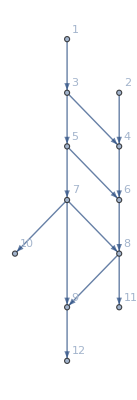

```mathematica
AdjacencyGraph[Data["Vertices List"],Data["Adjacency Matrix"],VertexLabels->"Name"]
```

```mathematica
MFGEquations=DataToEquations[Data/.{I1->1,I2->2,U1->1,U2->2, U3->3}];//Timing
MFGEquations["jvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort
MFGEquations["uvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort
```

DataToEquations: Triangle inequalities for switching costs: {}
DataToEquations: Reduced: True

The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: The system is:
NonNegative[-2+j310+j313-j331-jt349-jt352+jt361+jt364-jt367-jt370]&&NonNegative[j309]&&NonNegative[j310]&&NonNegative[j309+j331-jt361-jt364]&&NonNegative[j312]&&NonNegative[j313]&&NonNegative[j314]&&NonNegative[j315]&&NonNegative[j316]&&NonNegative[j317]&&NonNegative[3-j316-j319]&&NonNegative[j319]&&NonNegative[j316]&&NonNegative[3-j316-j319]&&NonNegative[j319]&&NonNegative[j309-jt349-jt352]&&NonNegative[-3+j310+j313-j331+jt361+jt364-jt367-jt370]&&NonNegative[j309-j313+j331-jt361-jt364+jt367+jt370]&&NonNegative[-3+j310+j312+j313-j331-jt367-jt370]&&NonNegative[j331]&&NonNegative[-3+j312+j313-j331]&&NonNegative[-j312+j314+j315+j316-j317+j319+j331-jt397-jt400]&&NonNegative[j317-j319+jt397+jt400]&&NonNegative[j315-jt397-jt400]&&NonNegative[1-jt349]&&NonNegative[jt349]&&NonNegative[-jt352]&&NonNegative[j309-jt349]&&NonNegative[jt352]&&NonNegative[-3+j310+j313-j331-jt352+jt361+jt364-jt367-jt370]&&NonNegative[2-jt355]&&NonNegative[jt355]&&NonNegative[-2+j313-j331-jt349-jt352+jt355+jt361+jt364-jt367-jt370]&&NonNegative[j310-jt355]&&NonNegative[2-j313+j331+jt349+jt352-jt355-jt361-jt364+jt367+jt370]&&NonNegative[-2+j309-jt349-jt352+jt355]&&NonNegative[j309-jt361]&&NonNegative[jt361]&&NonNegative[-3+j310+j313-j331+jt361-jt367-jt370]&&NonNegative[j312-jt361]&&NonNegative[jt364]&&NonNegative[j331-jt364]&&NonNegative[j310-jt367]&&NonNegative[jt367]&&NonNegative[j309-j313+j331-jt361-jt364+jt367]&&NonNegative[j313-jt367]&&NonNegative[jt370]&&NonNegative[-3+j312+j313-j331-jt370]&&NonNegative[jt372]&&NonNegative[jt373]&&NonNegative[j312-jt372-jt373]&&NonNegative[j314+j315+j331-jt372-jt373-jt376-jt378-jt379]&&NonNegative[jt376]&&NonNegative[-j312+j316-j317+j319+jt372+jt373+jt378+jt379-jt397-jt400]&&NonNegative[jt378]&&NonNegative[jt379]&&NonNegative[j317-j319-jt378-jt379+jt397+jt400]&&NonNegative[-j314-j315+jt372+jt373+jt376+jt379]&&NonNegative[j314-jt372-jt379]&&NonNegative[j315-jt373-jt376]&&NonNegative[jt384]&&NonNegative[jt385]&&NonNegative[j313-jt384-jt385]&&NonNegative[-3+j313+j314+j315+j316+j319-jt384-jt385-jt388-jt390-jt391-jt397-jt400]&&NonNegative[jt388]&&NonNegative[3-j313-j315-j316-j319+jt384+jt385+jt390+jt391+jt397+jt400]&&NonNegative[jt390]&&NonNegative[jt391]&&NonNegative[j315-jt390-jt391-jt397-jt400]&&NonNegative[j312-j314-j315-j316-j319-j331+jt384+jt385+jt388+jt391+jt397+jt400]&&NonNegative[-j312+j314+j315+j316-j317+j319+j331-jt384-jt391-jt397-jt400]&&NonNegative[j317-jt385-jt388]&&NonNegative[j315-jt397]&&NonNegative[jt397]&&NonNegative[j317-j319+jt397]&&NonNegative[j319-jt397]&&NonNegative[jt400]&&NonNegative[-jt400]&&NonNegative[j316]&&NonNegative[3-j316-j319]&&NonNegative[j319]&&NonNegative[1-u408+u410]&&NonNegative[1-u408+u411]&&NonNegative[-1+u408-u410]&&NonNegative[-u410+u411]&&NonNegative[-1+u408-u411]&&NonNegative[u410-u411]&&NonNegative[4+j309-j310-j313+j331-jt361-jt364+jt367+jt370-u409+u410]&&NonNegative[2-u409+u412]&&NonNegative[-4-j309+j310+j313-j331+jt361+jt364-jt367-jt370+u409-u410]&&NonNegative[-2-j309+j310+j313-j331+jt361+jt364-jt367-jt370-u410+u412]&&NonNegative[-2+u409-u412]&&NonNegative[2+j309-j310-j313+j331-jt361-jt364+jt367+jt370+u410-u412]&&NonNegative[3+j309-j310-j313+j331-jt361-jt364+jt367+jt370-u411+u413]&&NonNegative[3+j309-j310-j313+j331-jt361-jt364+jt367+jt370-u411+u414]&&NonNegative[-3-j309+j310+j313-j331+jt361+jt364-jt367-jt370+u411-u413]&&NonNegative[-u413+u414]&&NonNegative[-3-j309+j310+j313-j331+jt361+jt364-jt367-jt370+u411-u414]&&NonNegative[u413-u414]&&NonNegative[-3-2 j309+2 j310+j312+2 j313-3 j331+2 jt361+2 jt364-2 jt367-2 jt370-u412+u413]&&NonNegative[-j309+j310+j313-j331+jt361+jt364-jt367-jt370-u412+u415]&&NonNegative[3+2 j309-2 j310-j312-2 j313+3 j331-2 jt361-2 jt364+2 jt367+2 jt370+u412-u413]&&NonNegative[3+j309-j310-j312-j313+2 j331-jt361-jt364+jt367+jt370-u413+u415]&&NonNegative[j309-j310-j313+j331-jt361-jt364+jt367+jt370+u412-u415]&&NonNegative[-3-j309+j310+j312+j313-2 j331+jt361+jt364-jt367-jt370+u413-u415]&&NonNegative[j312-j331-u414+u416]&&NonNegative[j312-j331-u414+u417]&&NonNegative[j312-j331-u414+u418]&&NonNegative[-j312+j331+u414-u416]&&NonNegative[-u416+u417]&&NonNegative[-u416+u418]&&NonNegative[-j312+j331+u414-u417]&&NonNegative[u416-u417]&&NonNegative[-u417+u418]&&NonNegative[-j312+j331+u414-u418]&&NonNegative[u416-u418]&&NonNegative[u417-u418]&&NonNegative[3-2 j312+j315+j316-j317+j319+2 j331-jt397-jt400-u415+u416]&&NonNegative[3-j312+j331-u415+u419]&&NonNegative[3-j312+j331-u415+u420]&&NonNegative[-3+2 j312-j315-j316+j317-j319-2 j331+jt397+jt400+u415-u416]&&NonNegative[j312-j315-j316+j317-j319-j331+jt397+jt400-u416+u419]&&NonNegative[j312-j315-j316+j317-j319-j331+jt397+jt400-u416+u420]&&NonNegative[-3+j312-j331+u415-u419]&&NonNegative[-j312+j315+j316-j317+j319+j331-jt397-jt400+u416-u419]&&NonNegative[-u419+u420]&&NonNegative[-3+j312-j331+u415-u420]&&NonNegative[-j312+j315+j316-j317+j319+j331-jt397-jt400+u416-u420]&&NonNegative[u419-u420]&&NonNegative[2 j315-2 j317+j319-2 jt397-2 jt400-u417+u419]&&NonNegative[j315-j317+j319-jt397-jt400-u417+u421]&&NonNegative[-2 j315+2 j317-j319+2 jt397+2 jt400+u417-u419]&&NonNegative[-j315+j317+jt397+jt400-u419+u421]&&NonNegative[-j315+j317-j319+jt397+jt400+u417-u421]&&NonNegative[j315-j317-jt397-jt400+u419-u421]&&NonNegative[1+j316-u418]&&NonNegative[5-j316-j319-u420]&&NonNegative[3+j319-u421]&&(j309-jt349-jt352==0||-2+j310+j313-j331-jt349-jt352+jt361+jt364-jt367-jt370==0)&&(-3+j310+j313-j331+jt361+jt364-jt367-jt370==0||j309==0)&&(j309-j313+j331-jt361-jt364+jt367+jt370==0||j310==0)&&(-3+j310+j312+j313-j331-jt367-jt370==0||j309+j331-jt361-jt364==0)&&(j331==0||j312==0)&&(-3+j312+j313-j331==0||j313==0)&&(-j312+j314+j315+j316-j317+j319+j331-jt397-jt400==0||j314==0)&&(j317-j319+jt397+jt400==0||j315==0)&&(j315-jt397-jt400==0||j317==0)&&(1-jt349==0||-jt352==0)&&(jt349==0||jt352==0)&&(j309-jt349==0||-3+j310+j313-j331-jt352+jt361+jt364-jt367-jt370==0)&&(2-jt355==0||-2+j313-j331-jt349-jt352+jt355+jt361+jt364-jt367-jt370==0)&&(jt355==0||2-j313+j331+jt349+jt352-jt355-jt361-jt364+jt367+jt370==0)&&(j310-jt355==0||-2+j309-jt349-jt352+jt355==0)&&(j309-jt361==0||-3+j310+j313-j331+jt361-jt367-jt370==0)&&(jt361==0||jt364==0)&&(j312-jt361==0||j331-jt364==0)&&(j310-jt367==0||j309-j313+j331-jt361-jt364+jt367==0)&&(jt367==0||jt370==0)&&(j313-jt367==0||-3+j312+j313-j331-jt370==0)&&(jt372==0||j314+j315+j331-jt372-jt373-jt376-jt378-jt379==0)&&(jt373==0||jt378==0)&&(j312-jt372-jt373==0||-j314-j315+jt372+jt373+jt376+jt379==0)&&(jt376==0||jt379==0)&&(-j312+j316-j317+j319+jt372+jt373+jt378+jt379-jt397-jt400==0||j314-jt372-jt379==0)&&(j317-j319-jt378-jt379+jt397+jt400==0||j315-jt373-jt376==0)&&(jt384==0||-3+j313+j314+j315+j316+j319-jt384-jt385-jt388-jt390-jt391-jt397-jt400==0)&&(jt385==0||jt390==0)&&(j313-jt384-jt385==0||j312-j314-j315-j316-j319-j331+jt384+jt385+jt388+jt391+jt397+jt400==0)&&(jt388==0||jt391==0)&&(3-j313-j315-j316-j319+jt384+jt385+jt390+jt391+jt397+jt400==0||-j312+j314+j315+j316-j317+j319+j331-jt384-jt391-jt397-jt400==0)&&(j315-jt390-jt391-jt397-jt400==0||j317-jt385-jt388==0)&&(j315-jt397==0||j317-j319+jt397==0)&&(jt397==0||jt400==0)&&(j319-jt397==0||-jt400==0)&&(1-jt349==0||1-u408+u410==0)&&(jt349==0||1-u408+u411==0)&&(-jt352==0||-1+u408-u410==0)&&(j309-jt349==0||-u410+u411==0)&&(jt352==0||-1+u408-u411==0)&&(-3+j310+j313-j331-jt352+jt361+jt364-jt367-jt370==0||u410-u411==0)&&(2-jt355==0||4+j309-j310-j313+j331-jt361-jt364+jt367+jt370-u409+u410==0)&&(jt355==0||2-u409+u412==0)&&(-2+j313-j331-jt349-jt352+jt355+jt361+jt364-jt367-jt370==0||-4-j309+j310+j313-j331+jt361+jt364-jt367-jt370+u409-u410==0)&&(j310-jt355==0||-2-j309+j310+j313-j331+jt361+jt364-jt367-jt370-u410+u412==0)&&(2-j313+j331+jt349+jt352-jt355-jt361-jt364+jt367+jt370==0||-2+u409-u412==0)&&(-2+j309-jt349-jt352+jt355==0||2+j309-j310-j313+j331-jt361-jt364+jt367+jt370+u410-u412==0)&&(j309-jt361==0||3+j309-j310-j313+j331-jt361-jt364+jt367+jt370-u411+u413==0)&&(jt361==0||3+j309-j310-j313+j331-jt361-jt364+jt367+jt370-u411+u414==0)&&(-3+j310+j313-j331+jt361-jt367-jt370==0||-3-j309+j310+j313-j331+jt361+jt364-jt367-jt370+u411-u413==0)&&(j312-jt361==0||-u413+u414==0)&&(jt364==0||-3-j309+j310+j313-j331+jt361+jt364-jt367-jt370+u411-u414==0)&&(j331-jt364==0||u413-u414==0)&&(j310-jt367==0||-3-2 j309+2 j310+j312+2 j313-3 j331+2 jt361+2 jt364-2 jt367-2 jt370-u412+u413==0)&&(jt367==0||-j309+j310+j313-j331+jt361+jt364-jt367-jt370-u412+u415==0)&&(j309-j313+j331-jt361-jt364+jt367==0||3+2 j309-2 j310-j312-2 j313+3 j331-2 jt361-2 jt364+2 jt367+2 jt370+u412-u413==0)&&(j313-jt367==0||3+j309-j310-j312-j313+2 j331-jt361-jt364+jt367+jt370-u413+u415==0)&&(jt370==0||j309-j310-j313+j331-jt361-jt364+jt367+jt370+u412-u415==0)&&(-3+j312+j313-j331-jt370==0||-3-j309+j310+j312+j313-2 j331+jt361+jt364-jt367-jt370+u413-u415==0)&&(jt372==0||j312-j331-u414+u416==0)&&(jt373==0||j312-j331-u414+u417==0)&&(j312-jt372-jt373==0||j312-j331-u414+u418==0)&&(j314+j315+j331-jt372-jt373-jt376-jt378-jt379==0||-j312+j331+u414-u416==0)&&(jt376==0||-u416+u417==0)&&(-j312+j316-j317+j319+jt372+jt373+jt378+jt379-jt397-jt400==0||-u416+u418==0)&&(jt378==0||-j312+j331+u414-u417==0)&&(jt379==0||u416-u417==0)&&(j317-j319-jt378-jt379+jt397+jt400==0||-u417+u418==0)&&(-j314-j315+jt372+jt373+jt376+jt379==0||-j312+j331+u414-u418==0)&&(j314-jt372-jt379==0||u416-u418==0)&&(j315-jt373-jt376==0||u417-u418==0)&&(jt384==0||3-2 j312+j315+j316-j317+j319+2 j331-jt397-jt400-u415+u416==0)&&(jt385==0||3-j312+j331-u415+u419==0)&&(j313-jt384-jt385==0||3-j312+j331-u415+u420==0)&&(-3+j313+j314+j315+j316+j319-jt384-jt385-jt388-jt390-jt391-jt397-jt400==0||-3+2 j312-j315-j316+j317-j319-2 j331+jt397+jt400+u415-u416==0)&&(jt388==0||j312-j315-j316+j317-j319-j331+jt397+jt400-u416+u419==0)&&(3-j313-j315-j316-j319+jt384+jt385+jt390+jt391+jt397+jt400==0||j312-j315-j316+j317-j319-j331+jt397+jt400-u416+u420==0)&&(jt390==0||-3+j312-j331+u415-u419==0)&&(jt391==0||-j312+j315+j316-j317+j319+j331-jt397-jt400+u416-u419==0)&&(j315-jt390-jt391-jt397-jt400==0||-u419+u420==0)&&(j312-j314-j315-j316-j319-j331+jt384+jt385+jt388+jt391+jt397+jt400==0||-3+j312-j331+u415-u420==0)&&(-j312+j314+j315+j316-j317+j319+j331-jt384-jt391-jt397-jt400==0||-j312+j315+j316-j317+j319+j331-jt397-jt400+u416-u420==0)&&(j317-jt385-jt388==0||u419-u420==0)&&(j315-jt397==0||2 j315-2 j317+j319-2 jt397-2 jt400-u417+u419==0)&&(jt397==0||j315-j317+j319-jt397-jt400-u417+u421==0)&&(j317-j319+jt397==0||-2 j315+2 j317-j319+2 jt397+2 jt400+u417-u419==0)&&(j319-jt397==0||-j315+j317+jt397+jt400-u419+u421==0)&&(jt400==0||-j315+j317-j319+jt397+jt400+u417-u421==0)&&(-jt400==0||j315-j317-jt397-jt400+u419-u421==0)&&(j316==0||1+j316-u418==0)&&(3-j316-j319==0||5-j316-j319-u420==0)&&(j319==0||3+j319-u421==0)
and the rules are:
<|j306→1,j307→2,j308→-2+j310+j313-j331-jt349-jt352+jt361+jt364-jt367-jt370,j311→j309+j331-jt361-jt364,j318→3-j316-j319,j320→j316,j321→3-j316-j319,j322→j319,j323→1,j324→2,j325→0,j326→0,j327→j309-jt349-jt352,j328→-3+j310+j313-j331+jt361+jt364-jt367-jt370,j329→j309-j313+j331-jt361-jt364+jt367+jt370,j330→-3+j310+j312+j313-j331-jt367-jt370,j332→-3+j312+j313-j331,j333→-j312+j314+j315+j316-j317+j319+j331-jt397-jt400,j334→j317-j319+jt397+jt400,j335→0,j336→j315-jt397-jt400,j337→0,j338→0,j339→0,j340→0,j341→0,j342→0,j343→0,jt344→0,jt345→1,jt346→0,jt347→2,jt348→1-jt349,jt350→-jt352,jt351→j309-jt349,jt353→-3+j310+j313-j331-jt352+jt361+jt364-jt367-jt370,jt354→2-jt355,jt356→-2+j313-j331-jt349-jt352+jt355+jt361+jt364-jt367-jt370,jt357→j310-jt355,jt358→2-j313+j331+jt349+jt352-jt355-jt361-jt364+jt367+jt370,jt359→-2+j309-jt349-jt352+jt355,jt360→j309-jt361,jt362→-3+j310+j313-j331+jt361-jt367-jt370,jt363→j312-jt361,jt365→j331-jt364,jt366→j310-jt367,jt368→j309-j313+j331-jt361-jt364+jt367,jt369→j313-jt367,jt371→-3+j312+j313-j331-jt370,jt374→j312-jt372-jt373,jt375→j314+j315+j331-jt372-jt373-jt376-jt378-jt379,jt377→-j312+j316-j317+j319+jt372+jt373+jt378+jt379-jt397-jt400,jt380→j317-j319-jt378-jt379+jt397+jt400,jt381→-j314-j315+jt372+jt373+jt376+jt379,jt382→j314-jt372-jt379,jt383→j315-jt373-jt376,jt386→j313-jt384-jt385,jt387→-3+j313+j314+j315+j316+j319-jt384-jt385-jt388-jt390-jt391-jt397-jt400,jt389→3-j313-j315-j316-j319+jt384+jt385+jt390+jt391+jt397+jt400,jt392→j315-jt390-jt391-jt397-jt400,jt393→j312-j314-j315-j316-j319-j331+jt384+jt385+jt388+jt391+jt397+jt400,jt394→-j312+j314+j315+j316-j317+j319+j331-jt384-jt391-jt397-jt400,jt395→j317-jt385-jt388,jt396→j315-jt397,jt398→j317-j319+jt397,jt399→j319-jt397,jt401→-jt400,jt402→j316,jt403→0,jt404→3-j316-j319,jt405→0,jt406→j319,jt407→0,u422→1,u423→2,u424→3,u427→-1+u408,u428→-2+u409,u429→2+j309-j310-j313+j331-jt361-jt364+jt367+jt370+u410,u430→-3-j309+j310+j313-j331+jt361+jt364-jt367-jt370+u411,u431→j309-j310-j313+j331-jt361-jt364+jt367+jt370+u412,u432→-3-j309+j310+j312+j313-2 j331+jt361+jt364-jt367-jt370+u413,u433→-j312+j331+u414,u434→-3+j312-j331+u415,u435→-j312+j315+j316-j317+j319+j331-jt397-jt400+u416,u436→-j315+j317-j319+jt397+jt400+u417,u437→-j316+u418,u438→j315-j317-jt397-jt400+u419,u439→-3+j316+j319+u420,u440→-j319+u421,u441→1,u442→2,u443→3,u444→u408,u445→u409,u425→u408,u426→u409|>

$Aborted

Part::partw: Part 2 of MFGEquations[criticalreduced1] does not exist.

ReplaceAll::reps: {MFGEquations[criticalreduced1]⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

KeySort::invrl: The argument MFGEquations[jvars]/.MFGEquations[criticalreduced1]⟦2⟧ is not a valid Association or a list of rules.

KeySort[MFGEquations[jvars]/.MFGEquations[criticalreduced1]⟦2⟧]

Part::partw: Part 2 of MFGEquations[criticalreduced1] does not exist.

ReplaceAll::reps: {MFGEquations[criticalreduced1]⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

KeySort::invrl: The argument MFGEquations[uvars]/.MFGEquations[criticalreduced1]⟦2⟧ is not a valid Association or a list of rules.

KeySort[MFGEquations[uvars]/.MFGEquations[criticalreduced1]⟦2⟧]

```mathematica
MFGEquations["FG"]
```

MFGEquations[FG]

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.77;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],4,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],9,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```